## Analysis of Chromophore Organization in Various Light-Harvesting Complexes -- A Summary Work

In this study, we try to link the arrangements of light-harvesting complexs to their EET efficiency. We try to explain these results within our GFT extension. However, there are also some points that may not found simply by looking at the architechture of the complexes but are included in our theory. We list them below:

I. Things hard to see:
(i)* Whether EET occurs in a J-to-H fashion (To support this, one need to analyze local protein structure of the clustered dipoles ...; whether Chlb[higher transition energy] is more likely to have a J-like interaction in LHCII)

II. Things can be explained:
(i) Clustering of Chl's in RDF -- YES! A key point... Don't forget to look at the interaction distribution, which can help argue that EET are dominated by the strongly coupled clusters.
(ii) The clustered Chl's tend to be parallel or anti-parallel to each other (This couples the dimer) -- NO!! This doesn't seem to work, as the protein superstructure is constructed, the angle distribution lies quite dispersed...
(iii)* interaction-corrected angle distribution (We need to look at this because the angle distibution doesn't necessary indicate the sign of interaction, which in our theory is predicted a difference in EET rate)
(iv) More rapid EET from J-like to H-like clusters (Although the whole complex shows a complex network, the mean distance for J-H pair is significantly larger than J-J or H-H pair.)

III. Things to be worked out:
(i)* Implications in the Lambert plot -- intuition: the angle orientations of Chl's shouldn't be isotropic -- Q-Q plot
(ii)* Can we predict the direction of EET simply by the angular architecture of the clustered dipoles? (A comparative study is needed... Look at correlations...)
(iii)* The hierarchical structure analysis of the complexes ... (how?)

*: pending work...

Loading data: 2BHW (LHCII), 1JB0 (PSI), 1RWT (LHCII), 3ARC (PSII), 3PCQ (PSI), 3LW5 (PSI)
Note that the 3ARC data is quite strange ...

#### Read necessary data...

```mathematica
(* read Mg atomic locations from the PDB file *)
mg2BHWdata=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/2BHW_MG"]];
mg2BHW=raddf[mg2BHWdata];

(* read NB and ND info from this PDB file *)
nb=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/2BHW_NB"]];
nd=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/2BHW_ND"]];
d2BHWdata=Normalize/@(nb-nd);

mg1JB0data=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/1JB0_MG"]];
mg1JB0=raddf[mg1JB0data];

(* read NB and ND info from this PDB file *)
nb=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/1JB0_NB"]];
nd=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/1JB0_ND"]];
d1JB0data=Normalize/@(nb-nd);

mg1RWTdata=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/1RWT_MG"]];
mg1RWT=raddf[mg1RWTdata];

(* read NB and ND info from this PDB file *)
nb=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/1RWT_NB"]];
nd=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/1RWT_ND"]];
d1RWTdata=Normalize/@(nb-nd);

(* read Mg atomic locations from the PDB file *)
mg3ARCdata=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/3ARC_MG"]];
mg3ARC=raddf[mg3ARCdata];

(* read NB and ND info from this PDB file *)
nb=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/3ARC_NB"]];
nd=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/3ARC_ND"]];
d3ARCdata=Normalize/@(nb-nd);

mg3PCQdata=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/3PCQ_MG"]];
mg3PCQ=raddf[mg3PCQdata];

(* read NB and ND info from this PDB file *)
nb=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/3PCQ_NB"]];
nd=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/3PCQ_ND"]];
d3PCQdata=Normalize/@(nb-nd);

(* read Mg atomic locations from the PDB file *)
mg3LW5data=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/3LW5_MG"]];
mg3LW5=raddf[mg3LW5data];

(* read NB and ND info from this PDB file *)
nb=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/3LW5_NB"]];
nd=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/3LW5_ND"]];
d3LW5data=Normalize/@(nb-nd);
```

## Discussion on 8/31/2011

Some general results obtained:
	1. RDF showed structured peaks in various complexes (describe them to YC ...)
	2. It’s not straightforward to see key design method in dipole angular distributions (although when larger crystal structure is built, there’s symmetry in angular distributions)
		a. No special difference for mutual dipoles inheriting different interaction signs
		b. The number of dipoles of different interaction signs differ quite, but no special sign preference
	3. Only very limited interactions are strong (>100 wavenumber), suggesting the cluster-to-cluster EET is important for better efficiency
	4. Evidence suggesting J-H chromophore pair is the more likely channel for long range efficient EET
	5. The chromophores are clustered at about 6-7 units (very few have nearest chomophore further than 15 Å, pls check PSII)

Future work:
* isotropicity, rotational symmetry... (NO!)
* theoretical parts:
	0. discuss disorder effects
	1. include off-diagonal spectrum in eigenbasis
	2. adapt Redfield rate in defining efficiency
	3. use more straightforward change of parameters in the 4-site model 
* Dynamics in FMO, LHCII (include energetics)
* Clustering by defining cut-off interaction
	1. calculate the number of clustered chromophores
	2. check whether J-H pair is important for intercomplex EET
* 謀定而後動... ps. If there exist a more persuasive way of story telling, then do it; do not walk the easier but indirect road.

## Relative angle for dipoles that are separated around the second peak in the RDF

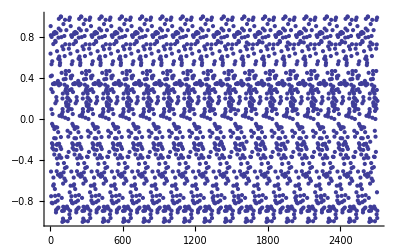

```mathematica
ListPlot[Apply[Dot,ds2[mg3LW5data,d3LW5data,20,1]⟦1⟧,1]]
```

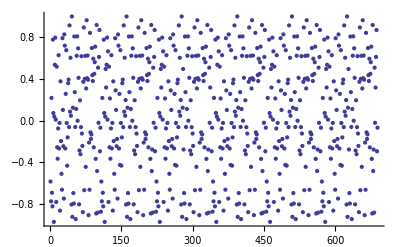

```mathematica
ListPlot[Apply[Dot,ds2[mg1JB0data,d1JB0data,20,1]⟦1⟧,1]]
```

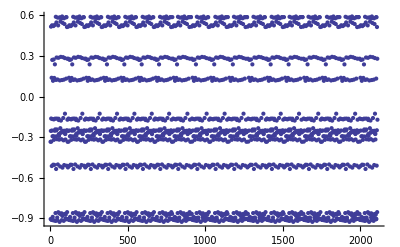

```mathematica
ListPlot[Apply[Dot,ds2[mg1RWTdata,d1RWTdata,20,1]⟦1⟧,1]]
```

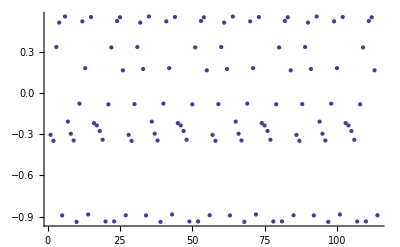

```mathematica
ListPlot[Apply[Dot,ds2[mg2BHWdata,d2BHWdata,20,1]⟦1⟧,1]]
```

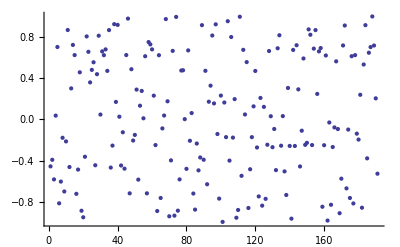

```mathematica
ListPlot[Apply[Dot,ds2[mg3ARCdata,d3ARCdata,20,1]⟦1⟧,1]]
```

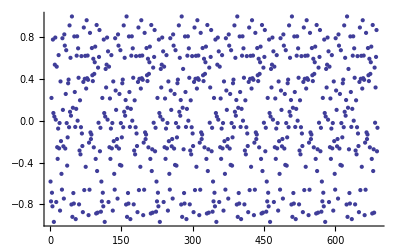

```mathematica
ListPlot[Apply[Dot,ds2[mg3PCQdata,d3PCQdata,20,1]⟦1⟧,1]]
```

## Relative angle for dipoles that are separated around the first peak in the RDF

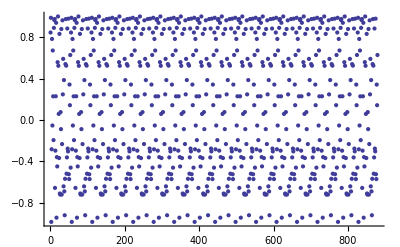

```mathematica
ListPlot[Apply[Dot,ds2[mg3LW5data,d3LW5data,10,1]⟦1⟧,1]]
```

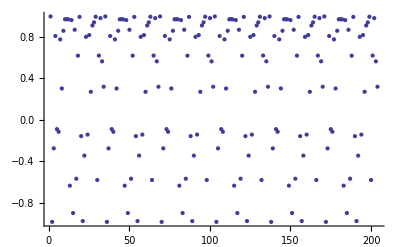

```mathematica
ListPlot[Apply[Dot,ds2[mg1JB0data,d1JB0data,10,1]⟦1⟧,1]]
```

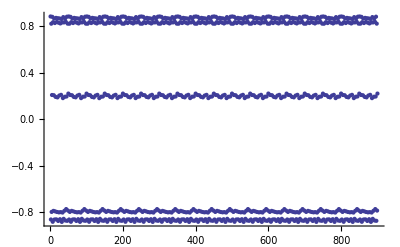

```mathematica
ListPlot[Apply[Dot,ds2[mg1RWTdata,d1RWTdata,10,1]⟦1⟧,1]]
```

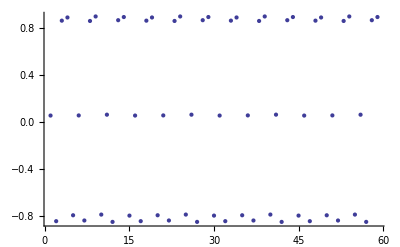

```mathematica
ListPlot[Apply[Dot,ds2[mg2BHWdata,d2BHWdata,10,1]⟦1⟧,1]]
```

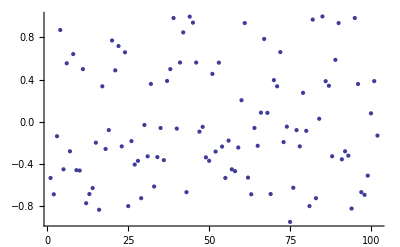

```mathematica
ListPlot[Apply[Dot,ds2[mg3ARCdata,d3ARCdata,10,1]⟦1⟧,1]]
```

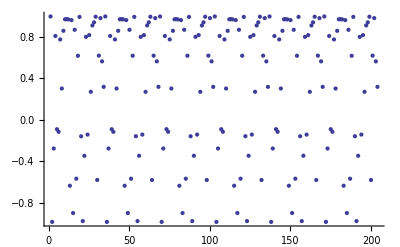

```mathematica
ListPlot[Apply[Dot,ds2[mg3PCQdata,d3PCQdata,10,1]⟦1⟧,1]]
```

## Distribution of "larger" dipole interaction and its relative frequency

```mathematica
temp1=coudf[mg3LW5data,d3LW5data];
temp2=Select[temp1,(#>100||#<-100)&];
freq=N[(Length@temp2/Length@temp1)*100,3];
Histogram[temp2,PlotLabel->freq "%"]
```

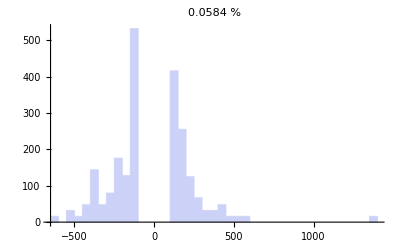

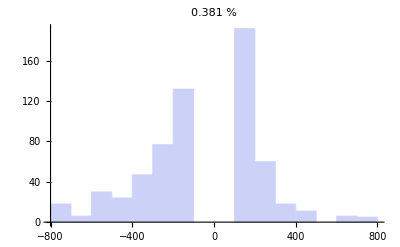

```mathematica
temp1=coudf[mg1JB0data,d1JB0data];
temp2=Select[temp1,(#>100||#<-100)&];
freq=N[(Length@temp2/Length@temp1)*100,3];
Histogram[temp2,PlotLabel->freq "%"]
```

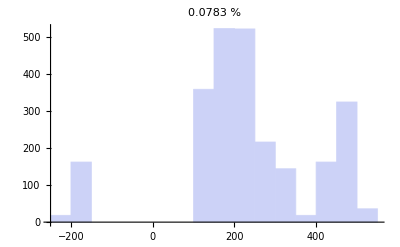

```mathematica
temp1=coudf[mg1RWTdata,d1RWTdata];
temp2=Select[temp1,(#>100||#<-100)&];
freq=N[(Length@temp2/Length@temp1)*100,3];
Histogram[temp2,PlotLabel->freq "%"]
```

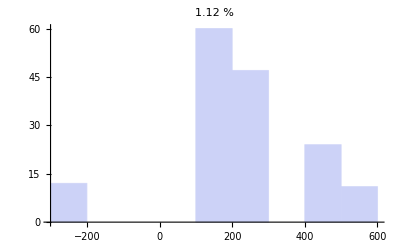

```mathematica
temp1=coudf[mg2BHWdata,d2BHWdata];
temp2=Select[temp1,(#>100||#<-100)&];
freq=N[(Length@temp2/Length@temp1)*100,3];
Histogram[temp2,PlotLabel->freq "%"]
```

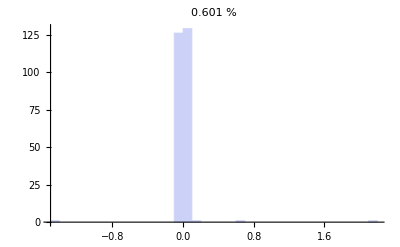

```mathematica
temp1=coudf[mg3ARCdata,d3ARCdata];
temp2=Select[temp1,(#>100||#<-100)&];
freq=N[(Length@temp2/Length@temp1)*100,3];
Histogram[temp2,PlotLabel->freq "%"]
```

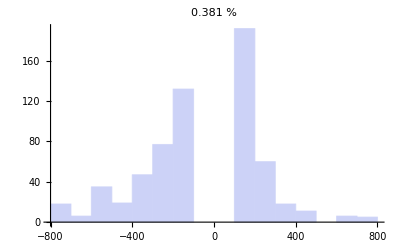

```mathematica
temp1=coudf[mg3PCQdata,d3PCQdata];
temp2=Select[temp1,(#>100||#<-100)&];
freq=N[(Length@temp2/Length@temp1)*100,3];
Histogram[temp2,PlotLabel->freq "%"]
```

## II-iv. RDF for +/- signed clusters (take its cluster-center-of-mass)

In our theory, the EET efficiency for minus-signed interaction to that of plus-signed is higher. To explore this difference, we analyse the chromophore distribution data for either interaction sign separately. What we found is that the mean distance of J-H pair is significantly larger than that of J-J or H-H pair. Hence, the EET in light-harvesting complex is likely to adapt the J-to-H fashion.

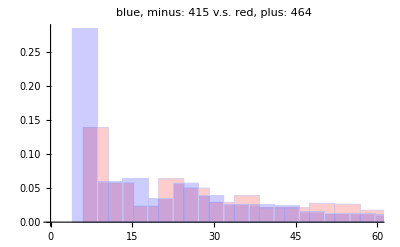

Mean distance of J-H pair: 200.545; Standard diviation: 80.3928

```mathematica
temp1=ds2[mg3LW5data,d3LW5data,10,1]⟦2⟧;
temp2=Flatten[Table[coudf[Table[{Part[mg3LW5data,temp1⟦i⟧],Part[d3LW5data,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦1⟧,Table[{Part[mg3LW5data,temp1⟦i⟧],Part[d3LW5data,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦2⟧],{j,1,Length@temp1}]];
minus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦1⟧//Flatten;
plus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦2⟧//Flatten;
pdis=Mean/@Table[Part[mg3LW5data,Part[temp1,plus]⟦i⟧],{i,1,Length@Part[temp1,plus]}];
mdis=Mean/@Table[Part[mg3LW5data,Part[temp1,minus]⟦i⟧],{i,1,Length@Part[temp1,minus]}];
Module[{text1=ToString@Length@pdis,text2=ToString@Length@mdis},Show[{rdf[Style[raddf@pdis,{Red,Opacity[0.2]}],100,60],rdf[Style[raddf@mdis,{Blue,Opacity[0.2]}],100,60]},PlotLabel->"blue, minus: "<>text1 <>" v.s. "<>"red, plus: "<>text2]]
sp=Flatten@Table[EuclideanDistance[pdis⟦i⟧,mdis⟦j⟧],{i,1,Length@pdis},{j,1,Length@mdis}];
Module[{m=Mean@sp,s=StandardDeviation@sp},Print["Mean distance of J-H pair: "<>ToString@m<>"; "<>"Standard diviation: "<>ToString@s]]
(*Histogram[sp,50,"Probability"]*)
```

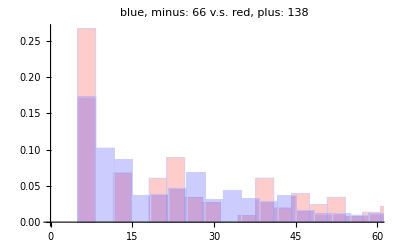

Mean distance of J-H pair: 142.167; Standard diviation: 73.4152

```mathematica
temp1=ds2[mg1JB0data,d1JB0data,10,1]⟦2⟧;
temp2=Flatten[Table[coudf[Table[{Part[mg1JB0data,temp1⟦i⟧],Part[d1JB0data,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦1⟧,Table[{Part[mg1JB0data,temp1⟦i⟧],Part[d1JB0data,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦2⟧],{j,1,Length@temp1}]];
minus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦1⟧//Flatten;
plus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦2⟧//Flatten;
pdis=Mean/@Table[Part[mg1JB0data,Part[temp1,plus]⟦i⟧],{i,1,Length@Part[temp1,plus]}];
mdis=Mean/@Table[Part[mg1JB0data,Part[temp1,minus]⟦i⟧],{i,1,Length@Part[temp1,minus]}];
Module[{text1=ToString@Length@pdis,text2=ToString@Length@mdis},Show[{rdf[Style[raddf@pdis,{Red,Opacity[0.2]}],100,60],rdf[Style[raddf@mdis,{Blue,Opacity[0.2]}],100,60]},PlotLabel->"blue, minus: "<>text1 <>" v.s. "<>"red, plus: "<>text2]]
sp=Flatten@Table[EuclideanDistance[pdis⟦i⟧,mdis⟦j⟧],{i,1,Length@pdis},{j,1,Length@mdis}];
Module[{m=Mean@sp,s=StandardDeviation@sp},Print["Mean distance of J-H pair: "<>ToString@m<>"; "<>"Standard diviation: "<>ToString@s]]
(*Histogram[sp,50,"Probability"]*)
```

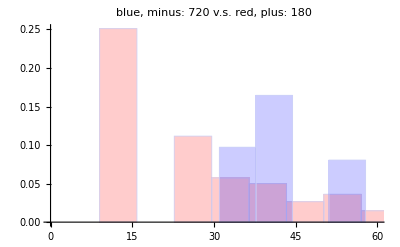

Mean distance of J-H pair: 285.699; Standard diviation: 138.328

```mathematica
temp1=ds2[mg1RWTdata,d1RWTdata,10,1]⟦2⟧;
temp2=Flatten[Table[coudf[Table[{Part[mg1RWTdata,temp1⟦i⟧],Part[d1RWTdata,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦1⟧,Table[{Part[mg1RWTdata,temp1⟦i⟧],Part[d1RWTdata,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦2⟧],{j,1,Length@temp1}]];
minus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦1⟧//Flatten;
plus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦2⟧//Flatten;
pdis=Mean/@Table[Part[mg1RWTdata,Part[temp1,plus]⟦i⟧],{i,1,Length@Part[temp1,plus]}];
mdis=Mean/@Table[Part[mg1RWTdata,Part[temp1,minus]⟦i⟧],{i,1,Length@Part[temp1,minus]}];
Module[{text1=ToString@Length@pdis,text2=ToString@Length@mdis},Show[{rdf[Style[raddf@pdis,{Red,Opacity[0.2]}],100,60],rdf[Style[raddf@mdis,{Blue,Opacity[0.2]}],100,60]},PlotLabel->"blue, minus: "<>text1 <>" v.s. "<>"red, plus: "<>text2]]
sp=Flatten@Table[EuclideanDistance[pdis⟦i⟧,mdis⟦j⟧],{i,1,Length@pdis},{j,1,Length@mdis}];
Module[{m=Mean@sp,s=StandardDeviation@sp},Print["Mean distance of J-H pair: "<>ToString@m<>"; "<>"Standard diviation: "<>ToString@s]]
(*Histogram[sp,50,"Probability"]*)
```

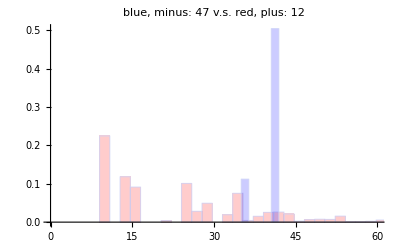

Mean distance of J-H pair: 87.9413; Standard diviation: 42.9112

```mathematica
temp1=ds2[mg2BHWdata,d2BHWdata,10,1]⟦2⟧;
temp2=Flatten[Table[coudf[Table[{Part[mg2BHWdata,temp1⟦i⟧],Part[d2BHWdata,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦1⟧,Table[{Part[mg2BHWdata,temp1⟦i⟧],Part[d2BHWdata,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦2⟧],{j,1,Length@temp1}]];
minus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦1⟧//Flatten;
plus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦2⟧//Flatten;
pdis=Mean/@Table[Part[mg2BHWdata,Part[temp1,plus]⟦i⟧],{i,1,Length@Part[temp1,plus]}];
mdis=Mean/@Table[Part[mg2BHWdata,Part[temp1,minus]⟦i⟧],{i,1,Length@Part[temp1,minus]}];
Module[{text1=ToString@Length@pdis,text2=ToString@Length@mdis},Show[{rdf[Style[raddf@pdis,{Red,Opacity[0.2]}],100,60],rdf[Style[raddf@mdis,{Blue,Opacity[0.2]}],100,60]},PlotLabel->"blue, minus: "<>text1 <>" v.s. "<>"red, plus: "<>text2]]
sp=Flatten@Table[EuclideanDistance[pdis⟦i⟧,mdis⟦j⟧],{i,1,Length@pdis},{j,1,Length@mdis}];
Module[{m=Mean@sp,s=StandardDeviation@sp},Print["Mean distance of J-H pair: "<>ToString@m<>"; "<>"Standard diviation: "<>ToString@s]]
(*Histogram[sp,50,"Probability"]*)
```

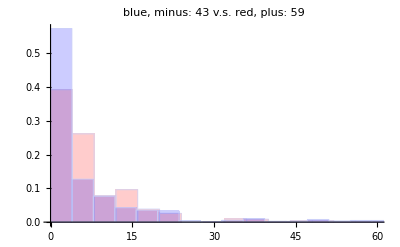

Mean distance of J-H pair: 165.075; Standard diviation: 80.9569

```mathematica
temp1=ds2[mg3ARCdata,d3ARCdata,10,1]⟦2⟧;
temp2=Flatten[Table[coudf[Table[{Part[mg3ARCdata,temp1⟦i⟧],Part[d3ARCdata,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦1⟧,Table[{Part[mg3ARCdata,temp1⟦i⟧],Part[d3ARCdata,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦2⟧],{j,1,Length@temp1}]];
minus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦1⟧//Flatten;
plus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦2⟧//Flatten;
pdis=Mean/@Table[Part[mg3ARCdata,Part[temp1,plus]⟦i⟧],{i,1,Length@Part[temp1,plus]}];
mdis=Mean/@Table[Part[mg3ARCdata,Part[temp1,minus]⟦i⟧],{i,1,Length@Part[temp1,minus]}];
Module[{text1=ToString@Length@pdis,text2=ToString@Length@mdis},Show[{rdf[Style[raddf@pdis,{Red,Opacity[0.2]}],100,60],rdf[Style[raddf@mdis,{Blue,Opacity[0.2]}],100,60]},PlotLabel->"blue, minus: "<>text1 <>" v.s. "<>"red, plus: "<>text2]]
sp=Flatten@Table[EuclideanDistance[pdis⟦i⟧,mdis⟦j⟧],{i,1,Length@pdis},{j,1,Length@mdis}];
Module[{m=Mean@sp,s=StandardDeviation@sp},Print["Mean distance of J-H pair: "<>ToString@m<>"; "<>"Standard diviation: "<>ToString@s]]
(*Histogram[sp,50,"Probability"]*)
```

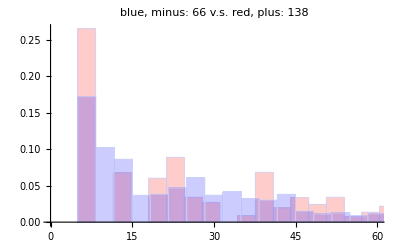

Mean distance of J-H pair: 141.933; Standard diviation: 73.3788

```mathematica
temp1=ds2[mg3PCQdata,d3PCQdata,10,1]⟦2⟧;
temp2=Flatten[Table[coudf[Table[{Part[mg3PCQdata,temp1⟦i⟧],Part[d3PCQdata,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦1⟧,Table[{Part[mg3PCQdata,temp1⟦i⟧],Part[d3PCQdata,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦2⟧],{j,1,Length@temp1}]];
minus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦1⟧//Flatten;
plus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦2⟧//Flatten;
pdis=Mean/@Table[Part[mg3PCQdata,Part[temp1,plus]⟦i⟧],{i,1,Length@Part[temp1,plus]}];
mdis=Mean/@Table[Part[mg3PCQdata,Part[temp1,minus]⟦i⟧],{i,1,Length@Part[temp1,minus]}];
Module[{text1=ToString@Length@pdis,text2=ToString@Length@mdis},Show[{rdf[Style[raddf@pdis,{Red,Opacity[0.2]}],100,60],rdf[Style[raddf@mdis,{Blue,Opacity[0.2]}],100,60]},PlotLabel->"blue, minus: "<>text1 <>" v.s. "<>"red, plus: "<>text2]]
sp=Flatten@Table[EuclideanDistance[pdis⟦i⟧,mdis⟦j⟧],{i,1,Length@pdis},{j,1,Length@mdis}];
Module[{m=Mean@sp,s=StandardDeviation@sp},Print["Mean distance of J-H pair: "<>ToString@m<>"; "<>"Standard diviation: "<>ToString@s]]
(*Histogram[sp,50,"Probability"]*)
```

## Anglar distribution for clusters and for clusters of different interaction sign

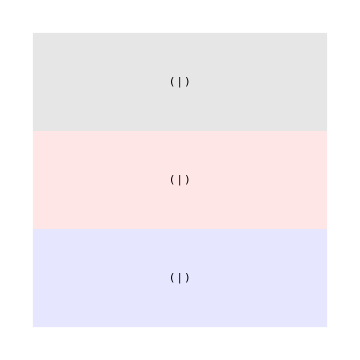

```mathematica
temp1=ds2[mg3LW5data,d3LW5data,10,1]⟦2⟧;
temp2=Flatten[Table[coudf[Table[{Part[mg3LW5data,temp1⟦i⟧],Part[d3LW5data,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦1⟧,Table[{Part[mg3LW5data,temp1⟦i⟧],Part[d3LW5data,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦2⟧],{j,1,Length@temp1}]];
minus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦1⟧//Flatten;
plus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦2⟧//Flatten;
GraphicsColumn[{Flatten[Table[Part[d3LW5data,temp1⟦i⟧],{i,1,Length@temp1}],1]//lambertplot,
Flatten[Table[Part[d3LW5data,Part[temp1,plus]⟦i⟧],{i,1,Length@Part[temp1,plus]}],1]//lambertplot,
Flatten[Table[Part[d3LW5data,Part[temp1,minus]⟦i⟧],{i,1,Length@Part[temp1,minus]}],1]//lambertplot},ImageSize->Medium,Background->{Lighter[Black,.9],Lighter[Red,.9],Lighter[Blue,.9]},AspectRatio->1]
```

```mathematica
temp1=ds2[mg1JB0data,d1JB0data,10,1]⟦2⟧;
temp2=Flatten[Table[coudf[Table[{Part[mg1JB0data,temp1⟦i⟧],Part[d1JB0data,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦1⟧,Table[{Part[mg1JB0data,temp1⟦i⟧],Part[d1JB0data,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦2⟧],{j,1,Length@temp1}]];
minus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦1⟧//Flatten;
plus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦2⟧//Flatten;GraphicsColumn[{Flatten[Table[Part[d1JB0data,temp1⟦i⟧],{i,1,Length@temp1}],1]//lambertplot,
Flatten[Table[Part[d1JB0data,Part[temp1,plus]⟦i⟧],{i,1,Length@Part[temp1,plus]}],1]//lambertplot,
Flatten[Table[Part[d1JB0data,Part[temp1,minus]⟦i⟧],{i,1,Length@Part[temp1,minus]}],1]//lambertplot},ImageSize->Medium,Background->{Lighter[Black,.9],Lighter[Red,.9],Lighter[Blue,.9]},AspectRatio->1]
```

-Graphics-

```mathematica
temp1=ds2[mg1RWTdata,d1RWTdata,10,1]⟦2⟧;
temp2=Flatten[Table[coudf[Table[{Part[mg1RWTdata,temp1⟦i⟧],Part[d1RWTdata,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦1⟧,Table[{Part[mg1RWTdata,temp1⟦i⟧],Part[d1RWTdata,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦2⟧],{j,1,Length@temp1}]];
minus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦1⟧//Flatten;
plus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦2⟧//Flatten;GraphicsColumn[{Flatten[Table[Part[d1RWTdata,temp1⟦i⟧],{i,1,Length@temp1}],1]//lambertplot,
Flatten[Table[Part[d1RWTdata,Part[temp1,plus]⟦i⟧],{i,1,Length@Part[temp1,plus]}],1]//lambertplot,
Flatten[Table[Part[d1RWTdata,Part[temp1,minus]⟦i⟧],{i,1,Length@Part[temp1,minus]}],1]//lambertplot},ImageSize->Medium,Background->{Lighter[Black,.9],Lighter[Red,.9],Lighter[Blue,.9]},AspectRatio->1]
```

-Graphics-

```mathematica
temp1=ds2[mg2BHWdata,d2BHWdata,10,1]⟦2⟧;
temp2=Flatten[Table[coudf[Table[{Part[mg2BHWdata,temp1⟦i⟧],Part[d2BHWdata,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦1⟧,Table[{Part[mg2BHWdata,temp1⟦i⟧],Part[d2BHWdata,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦2⟧],{j,1,Length@temp1}]];
minus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦1⟧//Flatten;
plus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦2⟧//Flatten;GraphicsColumn[{Flatten[Table[Part[d2BHWdata,temp1⟦i⟧],{i,1,Length@temp1}],1]//lambertplot,
Flatten[Table[Part[d2BHWdata,Part[temp1,plus]⟦i⟧],{i,1,Length@Part[temp1,plus]}],1]//lambertplot,
Flatten[Table[Part[d2BHWdata,Part[temp1,minus]⟦i⟧],{i,1,Length@Part[temp1,minus]}],1]//lambertplot},ImageSize->Medium,Background->{Lighter[Black,.9],Lighter[Red,.9],Lighter[Blue,.9]},AspectRatio->1]
```

-Graphics-

```mathematica
temp1=ds2[mg3ARCdata,d3ARCdata,10,1]⟦2⟧;
temp2=Flatten[Table[coudf[Table[{Part[mg3ARCdata,temp1⟦i⟧],Part[d3ARCdata,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦1⟧,Table[{Part[mg3ARCdata,temp1⟦i⟧],Part[d3ARCdata,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦2⟧],{j,1,Length@temp1}]];
minus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦1⟧//Flatten;
plus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦2⟧//Flatten;GraphicsColumn[{Flatten[Table[Part[d3ARCdata,temp1⟦i⟧],{i,1,Length@temp1}],1]//lambertplot,
Flatten[Table[Part[d3ARCdata,Part[temp1,plus]⟦i⟧],{i,1,Length@Part[temp1,plus]}],1]//lambertplot,
Flatten[Table[Part[d3ARCdata,Part[temp1,minus]⟦i⟧],{i,1,Length@Part[temp1,minus]}],1]//lambertplot},ImageSize->Medium,Background->{Lighter[Black,.9],Lighter[Red,.9],Lighter[Blue,.9]},AspectRatio->1]
```

-Graphics-

```mathematica
temp1=ds2[mg3PCQdata,d3PCQdata,10,1]⟦2⟧;
temp2=Flatten[Table[coudf[Table[{Part[mg3PCQdata,temp1⟦i⟧],Part[d3PCQdata,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦1⟧,Table[{Part[mg3PCQdata,temp1⟦i⟧],Part[d3PCQdata,temp1⟦i⟧]},{i,1,Length@temp1}]⟦j⟧⟦2⟧],{j,1,Length@temp1}]];
minus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦1⟧//Flatten;
plus=Reap[Table[If[temp2⟦i⟧<0,Sow[i,a],Sow[i,b]],{i,1,Length@temp1}];,{a,b}]⟦2⟧⟦2⟧//Flatten;GraphicsColumn[{Flatten[Table[Part[d3PCQdata,temp1⟦i⟧],{i,1,Length@temp1}],1]//lambertplot,
Flatten[Table[Part[d3PCQdata,Part[temp1,plus]⟦i⟧],{i,1,Length@Part[temp1,plus]}],1]//lambertplot,
Flatten[Table[Part[d3PCQdata,Part[temp1,minus]⟦i⟧],{i,1,Length@Part[temp1,minus]}],1]//lambertplot},ImageSize->Medium,Background->{Lighter[Black,.9],Lighter[Red,.9],Lighter[Blue,.9]},AspectRatio->1]
```

-Graphics-

## Dipole angular distrbution analysis for a single symmetry unit

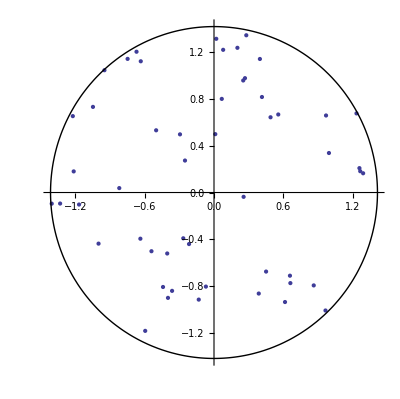
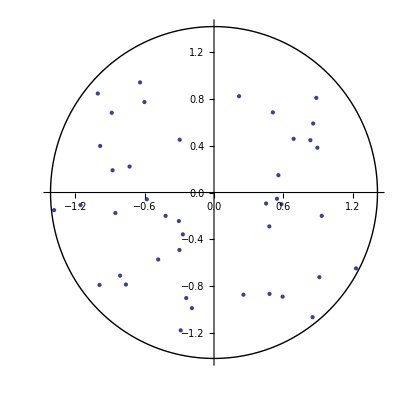

```mathematica
(* 1JB0 *)
nb=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/1JB0_s_NB"]];
nd=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/1JB0_s_ND"]];
d1JB0sdata=Normalize/@(nb-nd);
lambertplot[d1JB0sdata]
```

## Clustered chomophores are not dimers

#### In this part, one will see that dimers are not the best description for clustered chromophores. The clustering number for usual light-harvesting complexes are at about

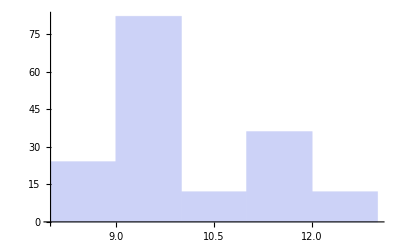

The number of clustered chromophores is about 7.

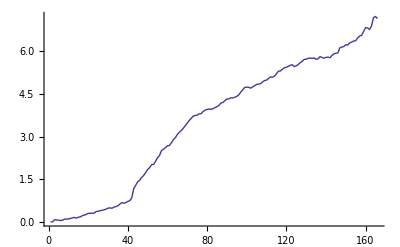

```mathematica
data=mg2BHWdata;
temp1=Table[Norm[data⟦i⟧-data⟦j⟧],{i,1,Length[data]},{j,1,Length[data]}];
Table[temp2[k]=Ordering[temp1⟦k⟧];,{k,1,Length@data}];
nearest[k_,l_]:=temp1⟦k⟧⟦temp2[k]⟧⟦l⟧
Histogram[Table[nearest[i,2],{i,1,Length@data}]]
For[inc=1,Mean@Table[nearest[i,inc]/nearest[i,2],{i,1,Length@data}]<2.,inc++];Print["The number of clustered chromophores is about "<>ToString[inc-1]<>"."]
ListPlot[Table[Variance[Table[nearest[i,k]/nearest[i,2],{i,1,Length@data}]],{k,1,Length@data}],Joined->True]
```

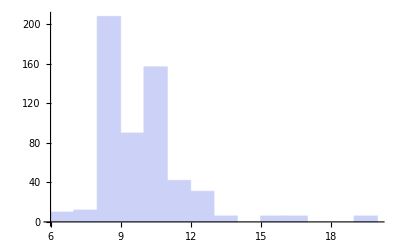

The number of clustered chromophores is about 6.

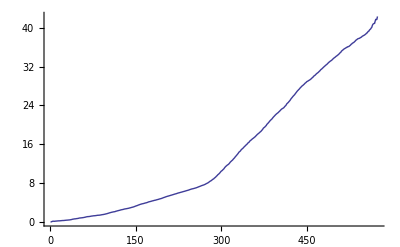

```mathematica
data=mg1JB0data;
temp1=Table[Norm[data⟦i⟧-data⟦j⟧],{i,1,Length[data]},{j,1,Length[data]}];
Table[temp2[k]=Ordering[temp1⟦k⟧];,{k,1,Length@data}];
nearest[k_,l_]:=temp1⟦k⟧⟦temp2[k]⟧⟦l⟧
Histogram[Table[nearest[i,2],{i,1,Length@data}]]
For[inc=1,Mean@Table[nearest[i,inc]/nearest[i,2],{i,1,Length@data}]<2.,inc++];Print["The number of clustered chromophores is about "<>ToString[inc-1]<>"."]
ListPlot[Table[Variance[Table[nearest[i,k]/nearest[i,2],{i,1,Length@data}]],{k,1,Length@data}],Joined->True]
```

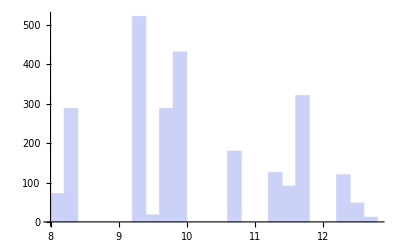

The number of clustered chromophores is about 7.

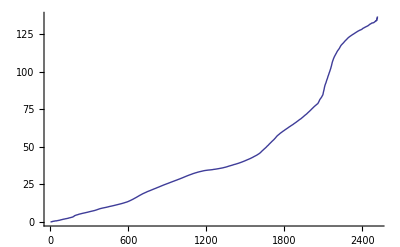

```mathematica
data=mg1RWTdata;
temp1=Table[Norm[data⟦i⟧-data⟦j⟧],{i,1,Length[data]},{j,1,Length[data]}];
Table[temp2[k]=Ordering[temp1⟦k⟧];,{k,1,Length@data}];
nearest[k_,l_]:=temp1⟦k⟧⟦temp2[k]⟧⟦l⟧
Histogram[Table[nearest[i,2],{i,1,Length@data}]]
For[inc=1,Mean@Table[nearest[i,inc]/nearest[i,2],{i,1,Length@data}]<2.,inc++];Print["The number of clustered chromophores is about "<>ToString[inc-1]<>"."]
ListPlot[Table[Variance[Table[nearest[i,k]/nearest[i,2],{i,1,Length@data}]],{k,1,Length@data}],Joined->True]
```

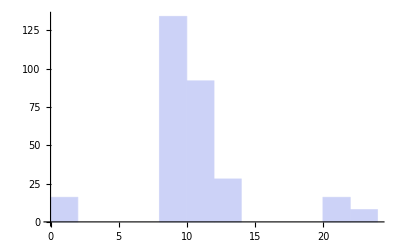

The number of clustered chromophores is about 2.

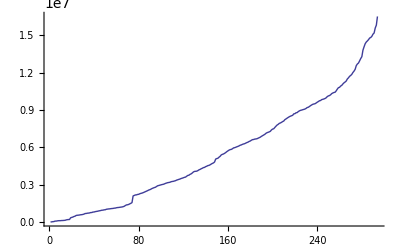

```mathematica
data=mg3ARCdata;
temp1=Table[Norm[data⟦i⟧-data⟦j⟧],{i,1,Length[data]},{j,1,Length[data]}];
Table[temp2[k]=Ordering[temp1⟦k⟧];,{k,1,Length@data}];
nearest[k_,l_]:=temp1⟦k⟧⟦temp2[k]⟧⟦l⟧
Histogram[Table[nearest[i,2],{i,1,Length@data}]]
For[inc=1,Mean@Table[nearest[i,inc]/nearest[i,2],{i,1,Length@data}]<2.,inc++];Print["The number of clustered chromophores is about "<>ToString[inc-1]<>"."]
ListPlot[Table[Variance[Table[nearest[i,k]/nearest[i,2],{i,1,Length@data}]],{k,1,Length@data}],Joined->True]
```

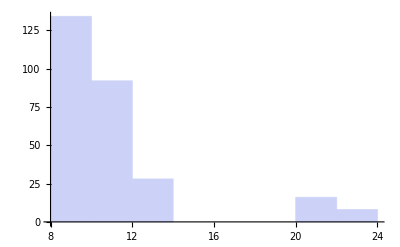

The number of clustered chromophores is about 6.

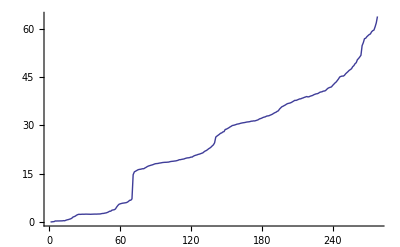

```mathematica
except=Reap[Table[If[nearest[k,2]<5,Sow[k]],{k,1,Length@data}];]⟦2,1⟧;
data=Delete[data,Partition[except,1]];
temp1=Table[Norm[data⟦i⟧-data⟦j⟧],{i,1,Length[data]},{j,1,Length[data]}];
Table[temp2[k]=Ordering[temp1⟦k⟧];,{k,1,Length@data}];
nearest[k_,l_]:=temp1⟦k⟧⟦temp2[k]⟧⟦l⟧
Histogram[Table[nearest[i,2],{i,1,Length@data}]]
For[inc=1,Mean@Table[nearest[i,inc]/nearest[i,2],{i,1,Length@data}]<2.,inc++];
Print["The number of clustered chromophores is about "<>ToString[inc-1]<>"."]
ListPlot[Table[Variance[Table[nearest[i,k]/nearest[i,2],{i,1,Length@data}]],{k,1,Length@data}],Joined->True]
```

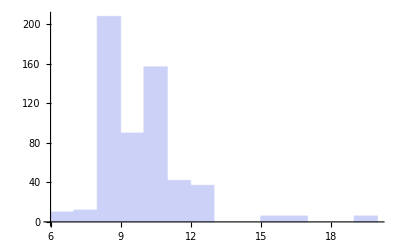

The number of clustered chromophores is about 6.

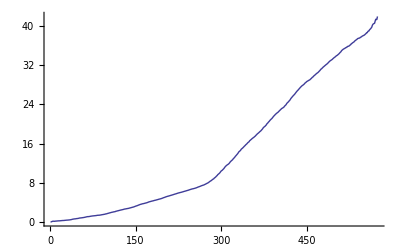

```mathematica
data=mg3PCQdata;
temp1=Table[Norm[data⟦i⟧-data⟦j⟧],{i,1,Length[data]},{j,1,Length[data]}];
Table[temp2[k]=Ordering[temp1⟦k⟧];,{k,1,Length@data}];
nearest[k_,l_]:=temp1⟦k⟧⟦temp2[k]⟧⟦l⟧
Histogram[Table[nearest[i,2],{i,1,Length@data}]]
For[inc=1,Mean@Table[nearest[i,inc]/nearest[i,2],{i,1,Length@data}]<2.,inc++];Print["The number of clustered chromophores is about "<>ToString[inc-1]<>"."]
ListPlot[Table[Variance[Table[nearest[i,k]/nearest[i,2],{i,1,Length@data}]],{k,1,Length@data}],Joined->True]
```

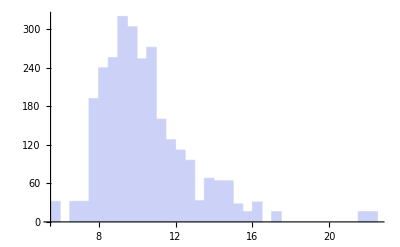

The number of clustered chromophores is about 6.

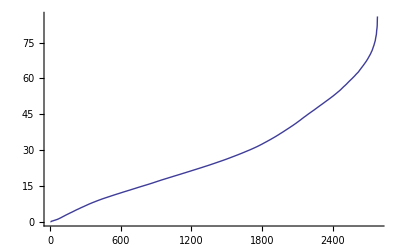

```mathematica
data=mg3LW5data;
temp1=Table[Norm[data⟦i⟧-data⟦j⟧],{i,1,Length[data]},{j,1,Length[data]}];
Table[temp2[k]=Ordering[temp1⟦k⟧];,{k,1,Length@data}];
nearest[k_,l_]:=temp1⟦k⟧⟦temp2[k]⟧⟦l⟧
Histogram[Table[nearest[i,2],{i,1,Length@data}]]
For[inc=1,Mean@Table[nearest[i,inc]/nearest[i,2],{i,1,Length@data}]<2.,inc++];Print["The number of clustered chromophores is about "<>ToString[inc-1]<>"."]
ListPlot[Table[Variance[Table[nearest[i,k]/nearest[i,2],{i,1,Length@data}]],{k,1,Length@data}],Joined->True]
```

```mathematica
`
```

## Clustering via interaction cut-off

```mathematica
ds3z2BHW=ParallelTable[ds3[mg2BHWdata,d2BHWdata,k],{k,1.,300.,1.}];
Clear[ds3p,ds3m,ds3a,clusterp,clusterm,clustera]
ds3p[k_]:=ds3p[k]=ds3z2BHW⟦k,2,1,1⟧;
ds3m[k_]:=ds3m[k]=ds3z2BHW⟦k,2,2,1⟧;
ds3a[k_]:=ds3a[k]=Flatten[ds3z2BHW⟦k,2⟧,2];
clusterp[k_]:=clusterp[k]=Gather[ds3p[k],Length@Intersection[#1,#2]>0&];
clusterm[k_]:=clusterm[k]=Gather[ds3m[k],Length@Intersection[#1,#2]>0&];
clustera[k_]:=clustera[k]=Gather[ds3a[k],Length@Intersection[#1,#2]>0&];
ListPlot[Table[{k,Mean[Length/@Union@@@clustera[k]]},{k,1.,300,1.}],Joined->True]
```

```mathematica
ds3z=ParallelTable[ds3[mg1JB0data,d1JB0data,k],{k,10.,500.,1.}];
ParallelTable[
ds3p[k]=Flatten[ds3z⟦k⟧⟦2⟧⟦1⟧,1];
ds3m[k]=Flatten[ds3z⟦k⟧⟦2⟧⟦2⟧,1];
ds3a[k]=Join[ds3p[k],ds3m[k]];
clusterp[k]=Gather[ds3p[k],Length@Intersection[#1,#2]>0&];
clusterm[k]=Gather[ds3m[k],Length@Intersection[#1,#2]>0&];
clustera[k]=Gather[ds3a[k],Length@Intersection[#1,#2]>0&];,{k,10.,500.,1.}];
ListPlot[Table[Mean[Length/@Union@@@clustera[k]],{k,10.,500.,1.}],Joined->True]
```

Part::pspec: Part specification 4.6 is neither an integer nor a list of integers.

Part::partd: Part specification 4.6 ⟦ 1 ⟧ is longer than depth of object.

Part::pspec: Part specification 4.6 is neither an integer nor a list of integers.

Part::partd: Part specification 4.6 ⟦ 2 ⟧ is longer than depth of object.

Part::pspec: Part specification 4.6 is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Gather::list: List expected at position 1 in Gather[4.6 ⟦ 1 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[4.6 ⟦ 2 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[4.6 ⟦ 1, 4.6, 2 ⟧, Length[#1 ∩ #2] > 0 &].

General::stop: Further output of Gather :: list will be suppressed during this calculation.

Part::partd: Part specification 4.7 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::pspec: Part specification 1.1 is neither an integer nor a list of integers.

Part::partd: Part specification 1.1 ⟦ 1 ⟧ is longer than depth of object.

Part::pspec: Part specification 1.1 is neither an integer nor a list of integers.

Part::partd: Part specification 1.1 ⟦ 2 ⟧ is longer than depth of object.

Part::pspec: Part specification 1.1 is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Gather::list: List expected at position 1 in Gather[1.1 ⟦ 1 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[1.1 ⟦ 2 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[1.1 ⟦ 1, 1.1, 2 ⟧, Length[#1 ∩ #2] > 0 &].

General::stop: Further output of Gather :: list will be suppressed during this calculation.

Part::partd: Part specification 1.2 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::pspec: Part specification 8.1 is neither an integer nor a list of integers.

Part::partd: Part specification 8.1 ⟦ 1 ⟧ is longer than depth of object.

Part::pspec: Part specification 8.1 is neither an integer nor a list of integers.

Part::partd: Part specification 8.1 ⟦ 2 ⟧ is longer than depth of object.

Part::pspec: Part specification 8.1 is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Gather::list: List expected at position 1 in Gather[8.1 ⟦ 1 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[8.1 ⟦ 2 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[8.1 ⟦ 1, 8.1, 2 ⟧, Length[#1 ∩ #2] > 0 &].

General::stop: Further output of Gather :: list will be suppressed during this calculation.

Part::partd: Part specification 8.2 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::pspec: Part specification 11.6 is neither an integer nor a list of integers.

Part::partd: Part specification 11.6 ⟦ 1 ⟧ is longer than depth of object.

Part::pspec: Part specification 11.6 is neither an integer nor a list of integers.

Part::partd: Part specification 11.6 ⟦ 2 ⟧ is longer than depth of object.

Part::pspec: Part specification 11.6 is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Gather::list: List expected at position 1 in Gather[11.6 ⟦ 1 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[11.6 ⟦ 2 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[11.6 ⟦ 1, 11.6, 2 ⟧, Length[#1 ∩ #2] > 0 &].

General::stop: Further output of Gather :: list will be suppressed during this calculation.

Part::partd: Part specification 11.7 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::pspec: Part specification 15.1 is neither an integer nor a list of integers.

Part::partd: Part specification 15.1 ⟦ 1 ⟧ is longer than depth of object.

Part::pspec: Part specification 15.1 is neither an integer nor a list of integers.

Part::partd: Part specification 15.1 ⟦ 2 ⟧ is longer than depth of object.

Part::pspec: Part specification 15.1 is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Gather::list: List expected at position 1 in Gather[15.1 ⟦ 1 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[15.1 ⟦ 2 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[15.1 ⟦ 1, 15.1, 2 ⟧, Length[#1 ∩ #2] > 0 &].

General::stop: Further output of Gather :: list will be suppressed during this calculation.

Part::partd: Part specification 15.2 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::pspec: Part specification 18.6 is neither an integer nor a list of integers.

Part::partd: Part specification 18.6 ⟦ 1 ⟧ is longer than depth of object.

Part::pspec: Part specification 18.6 is neither an integer nor a list of integers.

Part::partd: Part specification 18.6 ⟦ 2 ⟧ is longer than depth of object.

Part::pspec: Part specification 18.6 is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Gather::list: List expected at position 1 in Gather[18.6 ⟦ 1 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[18.6 ⟦ 2 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[18.6 ⟦ 1, 18.6, 2 ⟧, Length[#1 ∩ #2] > 0 &].

General::stop: Further output of Gather :: list will be suppressed during this calculation.

Part::partd: Part specification 18.7 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::pspec: Part specification 22.1 is neither an integer nor a list of integers.

Part::partd: Part specification 22.1 ⟦ 1 ⟧ is longer than depth of object.

Part::pspec: Part specification 22.1 is neither an integer nor a list of integers.

Part::partd: Part specification 22.1 ⟦ 2 ⟧ is longer than depth of object.

Part::pspec: Part specification 22.1 is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Gather::list: List expected at position 1 in Gather[22.1 ⟦ 1 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[22.1 ⟦ 2 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[22.1 ⟦ 1, 22.1, 2 ⟧, Length[#1 ∩ #2] > 0 &].

General::stop: Further output of Gather :: list will be suppressed during this calculation.

Part::partd: Part specification 22.2 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::pspec: Part specification 25.6 is neither an integer nor a list of integers.

Part::partd: Part specification 25.6 ⟦ 1 ⟧ is longer than depth of object.

Part::pspec: Part specification 25.6 is neither an integer nor a list of integers.

Part::partd: Part specification 25.6 ⟦ 2 ⟧ is longer than depth of object.

Part::pspec: Part specification 25.6 is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Gather::list: List expected at position 1 in Gather[25.6 ⟦ 1 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[25.6 ⟦ 2 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[25.6 ⟦ 1, 25.6, 2 ⟧, Length[#1 ∩ #2] > 0 &].

General::stop: Further output of Gather :: list will be suppressed during this calculation.

Part::partd: Part specification 25.7 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::pspec: Part specification 29.1 is neither an integer nor a list of integers.

Part::partd: Part specification 29.1 ⟦ 1 ⟧ is longer than depth of object.

Part::pspec: Part specification 29.1 is neither an integer nor a list of integers.

Part::partd: Part specification 29.1 ⟦ 2 ⟧ is longer than depth of object.

Part::pspec: Part specification 29.1 is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Gather::list: List expected at position 1 in Gather[29.1 ⟦ 1 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[29.1 ⟦ 2 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[29.1 ⟦ 1, 29.1, 2 ⟧, Length[#1 ∩ #2] > 0 &].

General::stop: Further output of Gather :: list will be suppressed during this calculation.

Part::partd: Part specification 29.2 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::pspec: Part specification 32.6 is neither an integer nor a list of integers.

Part::partd: Part specification 32.6 ⟦ 1 ⟧ is longer than depth of object.

Part::pspec: Part specification 32.6 is neither an integer nor a list of integers.

Part::partd: Part specification 32.6 ⟦ 2 ⟧ is longer than depth of object.

Part::pspec: Part specification 32.6 is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::pspec: Part specification 36.1 is neither an integer nor a list of integers.

Gather::list: List expected at position 1 in Gather[32.6 ⟦ 1 ⟧, Length[#1 ∩ #2] > 0 &].

Part::partd: Part specification 36.1 ⟦ 1 ⟧ is longer than depth of object.

Gather::list: List expected at position 1 in Gather[32.6 ⟦ 2 ⟧, Length[#1 ∩ #2] > 0 &].

Part::pspec: Part specification 36.1 is neither an integer nor a list of integers.

Gather::list: List expected at position 1 in Gather[32.6 ⟦ 1, 32.6, 2 ⟧, Length[#1 ∩ #2] > 0 &].

Part::partd: Part specification 36.1 ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Gather :: list will be suppressed during this calculation.

Part::pspec: Part specification 36.1 is neither an integer nor a list of integers.

Part::partd: Part specification 32.7 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Gather::list: List expected at position 1 in Gather[36.1 ⟦ 1 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[36.1 ⟦ 2 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[36.1 ⟦ 1, 36.1, 2 ⟧, Length[#1 ∩ #2] > 0 &].

General::stop: Further output of Gather :: list will be suppressed during this calculation.

Part::partd: Part specification 36.2 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::pspec: Part specification 39.6 is neither an integer nor a list of integers.

Part::partd: Part specification 39.6 ⟦ 1 ⟧ is longer than depth of object.

Part::pspec: Part specification 39.6 is neither an integer nor a list of integers.

Part::partd: Part specification 39.6 ⟦ 2 ⟧ is longer than depth of object.

Part::pspec: Part specification 39.6 is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Gather::list: List expected at position 1 in Gather[39.6 ⟦ 1 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[39.6 ⟦ 2 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[39.6 ⟦ 1, 39.6, 2 ⟧, Length[#1 ∩ #2] > 0 &].

General::stop: Further output of Gather :: list will be suppressed during this calculation.

Part::partd: Part specification 39.7 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::pspec: Part specification 43.1 is neither an integer nor a list of integers.

Part::partd: Part specification 43.1 ⟦ 1 ⟧ is longer than depth of object.

Part::pspec: Part specification 43.1 is neither an integer nor a list of integers.

Part::partd: Part specification 43.1 ⟦ 2 ⟧ is longer than depth of object.

Part::pspec: Part specification 43.1 is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Gather::list: List expected at position 1 in Gather[43.1 ⟦ 1 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[43.1 ⟦ 2 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[43.1 ⟦ 1, 43.1, 2 ⟧, Length[#1 ∩ #2] > 0 &].

General::stop: Further output of Gather :: list will be suppressed during this calculation.

Part::partd: Part specification 43.2 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::pspec: Part specification 46.6 is neither an integer nor a list of integers.

Part::partd: Part specification 46.6 ⟦ 1 ⟧ is longer than depth of object.

Part::pspec: Part specification 46.6 is neither an integer nor a list of integers.

Part::partd: Part specification 46.6 ⟦ 2 ⟧ is longer than depth of object.

Part::pspec: Part specification 46.6 is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Gather::list: List expected at position 1 in Gather[46.6 ⟦ 1 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[46.6 ⟦ 2 ⟧, Length[#1 ∩ #2] > 0 &].

Gather::list: List expected at position 1 in Gather[46.6 ⟦ 1, 46.6, 2 ⟧, Length[#1 ∩ #2] > 0 &].

General::stop: Further output of Gather :: list will be suppressed during this calculation.

Part::partd: Part specification 46.7 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

-Graphics-

```mathematica
ds3z=ParallelTable[ds3[mg1RWTdata,d1RWTdata,k],{k,10.,500.,1.}];
ParallelTable[
ds3p[k]=Flatten[ds3z⟦k⟧⟦2⟧⟦1⟧,1];
ds3m[k]=Flatten[ds3z⟦k⟧⟦2⟧⟦2⟧,1];
ds3a[k]=Join[ds3p[k],ds3m[k]];
clusterp[k]=Gather[ds3p[k],Length@Intersection[#1,#2]>0&];
clusterm[k]=Gather[ds3m[k],Length@Intersection[#1,#2]>0&];
clustera[k]=Gather[ds3a[k],Length@Intersection[#1,#2]>0&];,{k,10.,500.,1.}];
ListPlot[Table[Mean[Length/@Union@@@clustera[k]],{k,10.,500.,1.}],Joined->True]
```

Part::partw: Part 575 of {{88.434, 120.74, 71.952}, {92.078, 144.328, 63.71}, {100.668, 148.286, 64.014}, {111.956, 147.338, 64.947}, {107.438, 146.217, 73.181}, « 42 », {99.49, 88.877, 65.812}, {87.652, 89.049, 65.849}, {91.604, 90.741, 74.081}, « 524 »} does not exist.

Part::partw: Part 575 of {{0.26903, 0.50661, 0.819127}, {0.653271, 0.276988, 0.704637}, {0.598877, 0.268276, 0.754569}, « 45 », {0.974218, -0.177153, 0.139702}, {-0.976305, 0.206094, 0.0659893}, « 524 »} does not exist.

Part::partw: Part 575 of {{88.434, 120.74, 71.952}, {92.078, 144.328, 63.71}, {100.668, 148.286, 64.014}, {111.956, 147.338, 64.947}, {107.438, 146.217, 73.181}, « 42 », {99.49, 88.877, 65.812}, {87.652, 89.049, 65.849}, {91.604, 90.741, 74.081}, « 524 »} does not exist.

Part::partw: Part 575 of {{0.26903, 0.50661, 0.819127}, {0.653271, 0.276988, 0.704637}, {0.598877, 0.268276, 0.754569}, « 45 », {0.974218, -0.177153, 0.139702}, {-0.976305, 0.206094, 0.0659893}, « 524 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 575 of {{88.434, 120.74, 71.952}, {92.078, 144.328, 63.71}, {100.668, 148.286, 64.014}, {111.956, 147.338, 64.947}, {107.438, 146.217, 73.181}, « 42 », {99.49, 88.877, 65.812}, {87.652, 89.049, 65.849}, {91.604, 90.741, 74.081}, « 524 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

$Aborted

$Aborted

-Graphics-

```mathematica
ds3z=ParallelTable[ds3[mg3PCQdata,d3PCQdata,k],{k,10.,500.,1.}];
ParallelTable[
ds3p[k]=Flatten[ds3z⟦k⟧⟦2⟧⟦1⟧,1];
ds3m[k]=Flatten[ds3z⟦k⟧⟦2⟧⟦2⟧,1];
ds3a[k]=Join[ds3p[k],ds3m[k]];
clusterp[k]=Gather[ds3p[k],Length@Intersection[#1,#2]>0&];
clusterm[k]=Gather[ds3m[k],Length@Intersection[#1,#2]>0&];
clustera[k]=Gather[ds3a[k],Length@Intersection[#1,#2]>0&];,{k,10.,500.,1.}];
ListPlot[Table[Mean[Length/@Union@@@clustera[k]],{k,10.,500.,1.}],Joined->True]
```

```mathematica
ds3z=ParallelTable[ds3[mg3LW5data,d3LW5data,k],{k,10.,500.,1.}];
ParallelTable[
ds3p[k]=Flatten[ds3z⟦k⟧⟦2⟧⟦1⟧,1];
ds3m[k]=Flatten[ds3z⟦k⟧⟦2⟧⟦2⟧,1];
ds3a[k]=Join[ds3p[k],ds3m[k]];
clusterp[k]=Gather[ds3p[k],Length@Intersection[#1,#2]>0&];
clusterm[k]=Gather[ds3m[k],Length@Intersection[#1,#2]>0&];
clustera[k]=Gather[ds3a[k],Length@Intersection[#1,#2]>0&];,{k,10.,500.,1.}];
ListPlot[Table[Mean[Length/@Union@@@clustera[k]],{k,10.,500.,1.}],Joined->True]
```